```mathematica
Needs["Constants`"]
Needs["Capture`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
Needs["Dielectrics`"]
```

Get::noopen: Cannot open Capture`.

Needs::nocont: Context Capture` was not created when Needs was evaluated.

$Failed

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIwiderm"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIwiderm"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIwiderm"];*)
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Interpolation test

```mathematica
SiO2eELDict[["f"]]=TestInterpolation[SiO2eELDict]
MgOeELDict[["f"]]=TestInterpolation[MgOeELDict]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

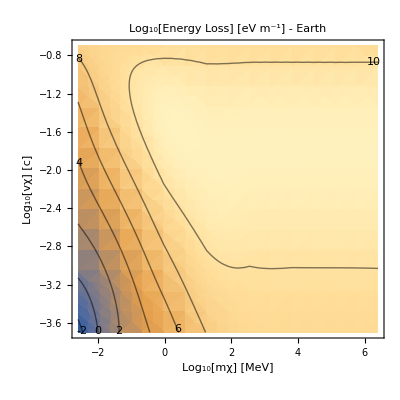

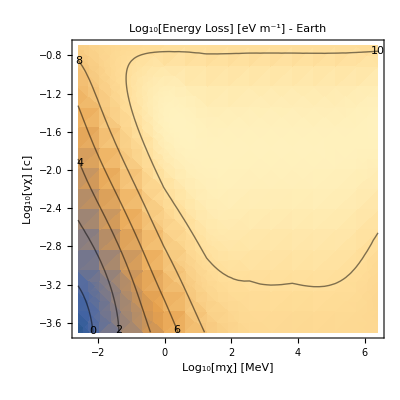

```mathematica
PlotEL[SiO2eELDict]
PlotEL[MgOeELDict]
```

#### EL functions

Organize into an EL function

Mantle

```mathematica
fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)
```

Core

```mathematica
fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=FeeELDict[["f"]][mχ,vχ]
```

```mathematica
FeeELDict[["f"]]
```

InterpolatingFunction[…]

```mathematica
FeNuc0ELDict[["f"]][-32.3,4.8]
FeNuc0ELDict[["f"]][-32.3,4.8]
```

-3.42349

### Test initialization functions

#### Propagating to the Earth

```mathematica
EK∞[mχ_,v∞_]:= 1/2 mχ (v∞)^2
```

```mathematica
E∞[mχ_,v∞_,r∞_,V_]:=EK∞[mχ,v∞]+V[r∞]
```

```mathematica
Vtest[r_]:=Gα/r
E∞[mχ,v∞,r∞,Vtest]
```

Gα/(r∞)+(mχ (v∞)^2)/2

```mathematica
vperp[v∞_,b∞_,r_]:=(b∞ v∞)/r
```

```mathematica
vr[mχ_,v∞_,b∞_,r∞_,V_,r_]:=√(2/mχ(E∞[mχ,v∞,r∞,V]-V[r])-vperp[v∞,b∞,r]^2)
```

```mathematica
vr[mχ,v∞,b∞,r∞,V,r]
```

√(-((b∞)^2 (v∞)^2)/r^2+(2 ((mχ (v∞)^2)/2-V[r]+V[r∞]))/mχ)

```mathematica
br[mχ_,v∞_,b∞_,r∞_,V_,r_]:=(b∞)/(√(1+(V[r∞]-V[r])/(EK∞[mχ,v∞])))
```

```mathematica
br[mχ,v∞,b∞,r∞,V,r]
```

(b∞)/(√(1+(2 (-V[r]+V[r∞]))/(mχ (v∞)^2)))

```mathematica
"G"/.SIConstRepl
```

6.67×10^-11

```mathematica
Vgrav[r_,mχ_] :=- (mχ("G"/.SIConstRepl)("ME"/.EarthRepl))/r
```

```mathematica
Vgrav[#,mχ]&
%[r]
```

Vgrav[#1,mχ]&

-(3.98199×10^14 mχ)/r

#### Example of Initial conditions

```mathematica
1/("rE"/.EarthRepl)br["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

0.499653

so barely changed, electrons are fast, but did decrease (which is the right direction)

```mathematica
vr["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

260048.

```mathematica
vperp["c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,"rE"/.EarthRepl]
```

150000.

#### Δr

```mathematica
Clear[Δrtest]
Δrtest[mχ_,vχ_,κ_,y_,consts_] :=(y 1/2 mχ vχ^2)/(κ^2 "JpereV"10^fELMantle[Log10[mχ], Log10[vχ]]) /.consts
```

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-9,10^-2,SIConstRepl]
%/("rE"/.EarthRepl)
```

1734.54

0.000272255

```mathematica
dE[rE_,bE_]:=2 √(rE^2-bE^2)
```

```mathematica
dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

1.10349×10^7

```mathematica
N[1/500]
```

0.002

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-10,10^-2,SIConstRepl]/dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

0.0157187

So at 10^-10mixing at electron mass and halo speeds, with b∞ = 1/2 rE, we are in intermediate scattering regime

#### Δr generalised (e only)

```mathematica
dc[bE_] := 2 √(rcore^2-bE^2)
dE[bE_] := 2 √(REarth^2-bE^2)
dM[bE_]:= If[rcore^2>bE^2,dE[bE] - dc[bE],Re[dE[bE]]]
```

```mathematica
dM[0]+dc[0]
REarth 2
```

1.2742×10^7

1.2742×10^7

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
ΔrAveraged[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
fΔrAveraged[mχ_,vχ_]:=Log10[ΔrAveraged[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

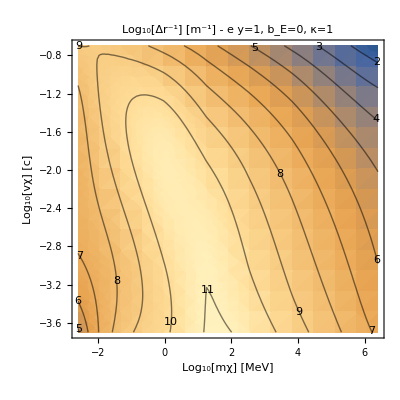

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveraged;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - e y=1, b_E=0, κ=1"]
]
```

#### Δr total 0 temperature

```mathematica
ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

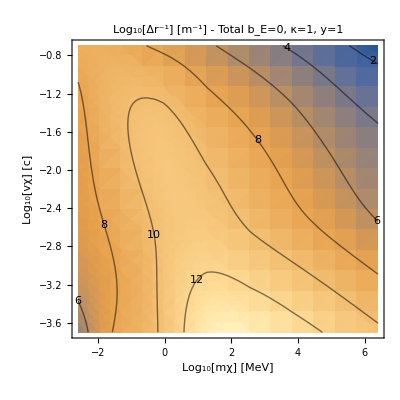

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveragedTot0;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=1"]
]
```

#### Explain boundary and peak (lowest kinetic energy above the fermi energy)

```mathematica
("EF")/("JpereV") /.FeeELDict[["fitparams"]]
("EF")/("JpereV") /.SiO2eELDict[["fitparams"]]
("EF")/("JpereV") /.MgOeELDict[["fitparams"]]
```

{8.0607,12.1265,20.9318,78.9,2030.5,42688.4}

{20.0443,58.1666}

{10.3207,18.4045,21.0279,50.3071}

```mathematica
((10^-2.5 "c")^2"m")/("JpereV") /.FeeELDict[["fitparams"]]
((10^-1.5 "c")^2 10^-2"m")/("JpereV") /.FeeELDict[["fitparams"]]
```

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

#### Interaction Length

```mathematica
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,
vχtemp,FeeELDict[["fitparams"]],βcore]& [1/2]];
(*NIntegrate[dσdEReNum[ω,mχtemp,vχtemp,FeTotalparams,βcore],{ω,0,ωmaxtemp}]*)
]
```

0.0262616

tesing cell input

```mathematica
σFe = 1.085089955014962*^13
```

1.08509×10^13

```mathematica
σtemp = 0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,vχtemp,FeTotalparams,βcore]& []];
(*σtemp = NIntegrate[dPdωeNum[ω,mχtemp,vχtemp,SiO2Totalparams],{ω,0,ωmaxtemp}]*)
]
```

0

```mathematica
lFe = κ^2("nI"/.SIcoreparams)σFe /.κ->10^-10(*approx, should really do density of each shell*)
```

1.52116×10^22

1.51848×10^15

0.

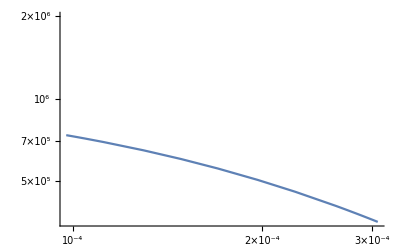

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
```

```mathematica
nIFromDensity[3580, "mN" /. SiNucCoeffs]
```

7.70224×10^28

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
SIcoreparams
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.1215×10^30,qF→3.2142×10^10,vF→3.72227×10^6,μ→6.31108×10^-18,ωp→5.97822×10^16,α→1/137,χ→0.432735,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→83.5454,nI→1.40188×10^29,Z→8,M→9.27329×10^-26,EF→6.31108×10^-18}

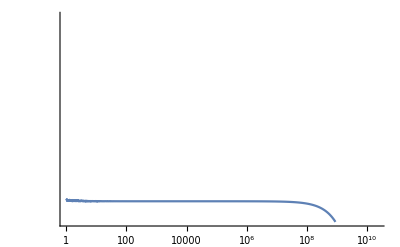

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcoreparams)|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
(*Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];*)
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
σtemp = 0;
Clear[SiNuc0σ]
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
```

1.51848×10^15

0.

2.90748×10^10

3.15401×10^16

```mathematica
((κ^2/.κ->10^-10)SiNuc0PTot)/((nIFromDensity[3580,"mN"/.SiNucCoeffs])("ℏ"/.SIConstRepl)(10^-3 "c"/.SIConstRepl))
```

0.000129382

9.5117×10^8

```mathematica
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
SiNuc0Pλ=(((κ^2/.κ->10^-10)SiNuc0PTot)/(10^-3 "c"/.SIConstRepl))^-1
```

2.90748×10^10

3.15401×10^16

9.5117×10^8

So from Nuclear Si at 0 temperature, the scattering length is large compared to the Earth

```mathematica
dPdωNuc0Num[# ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]& [1/2]
```

```mathematica
SiNucCoeffs
```

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26|>

```mathematica
FrontEndTokenExecute@"Save"
```